```mathematica
ClearAll["Global`*"];
```

```mathematica
path=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Sources/SwiftyStatsDemo/TestFiles"}];
```

{μ→-9.97833,β→3.03642}

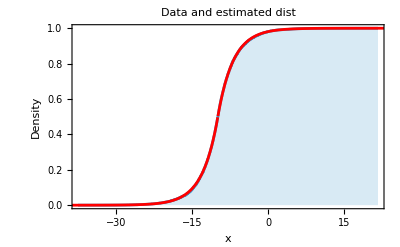

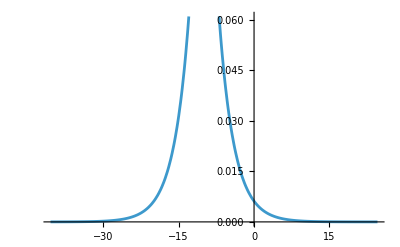

```mathematica
fileName=FileNameJoin[{path,"RND-Laplace.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, LaplaceDistribution[μ,β]]
dist=LaplaceDistribution[μ/.est,β/.est];
{xmin,xmax}={Min[data],Max[data]};
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,xmax+pad},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[PDF[dist,x],{x,xmin-pad,xmax+pad}]
```

{α→2.16646,β→0.593668}

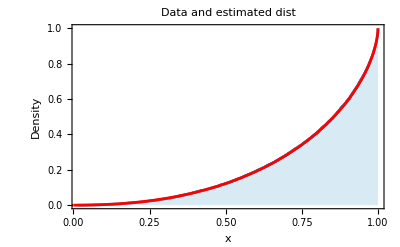

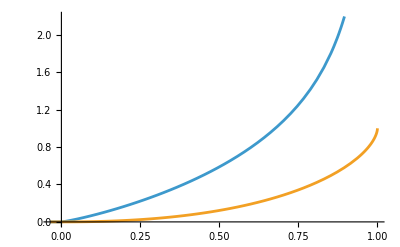

```mathematica
fileName=FileNameJoin[{path,"RND-beta.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, BetaDistribution[α,β]]
dist=BetaDistribution[α /.est, β /. est];
{xmin,xmax}={Min[data],Max[data]};
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,1},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[{PDF[dist,x],CDF[dist, x]},{x,xmin-pad,1}]
```

{α→0.321065,β→1.11134}

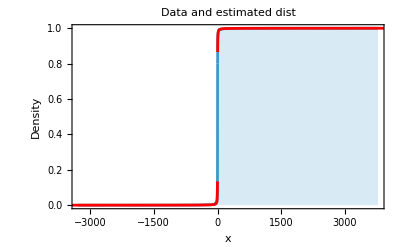

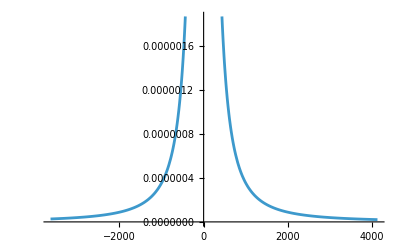

```mathematica
fileName=FileNameJoin[{path,"RND-cauchy.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, CauchyDistribution[α,β]]
dist=CauchyDistribution[α /.est, β /. est];
{xmin,xmax}={Min[data],Max[data]};
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,xmax+pad},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[PDF[dist,x],{x,xmin-pad,xmax+pad}]
```

{λ→2.51201}

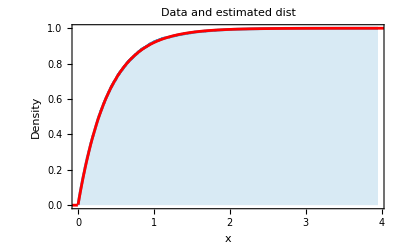

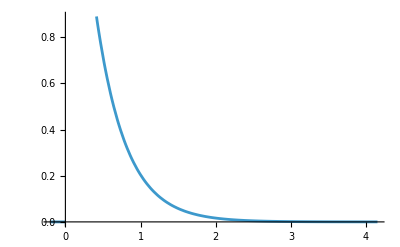

```mathematica
fileName=FileNameJoin[{path,"RND-exponential.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, ExponentialDistribution[λ]]
dist=ExponentialDistribution[λ /.est];
{xmin,xmax}={Min[data],Max[data]};
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,xmax+pad},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[PDF[dist,x],{x,xmin-pad,xmax+pad}]
```

{k→1.93694,θ→1.41213}

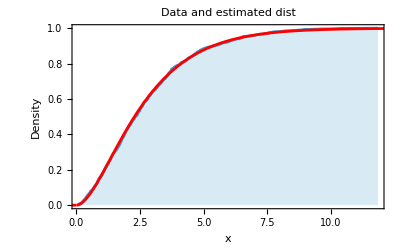

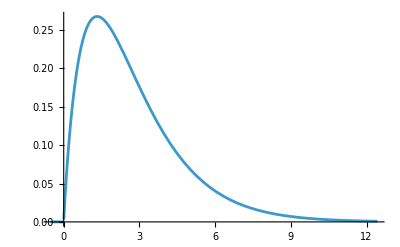

```mathematica
fileName=FileNameJoin[{path,"RND-gamma.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, GammaDistribution[k,θ]]
dist=GammaDistribution[k /.est,θ /.est];
{xmin,xmax}={Min[data],Max[data]};
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,xmax+pad},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[PDF[dist,x],{x,xmin-pad,xmax+pad}]
```

{k→3.01144,θ→1.99501}

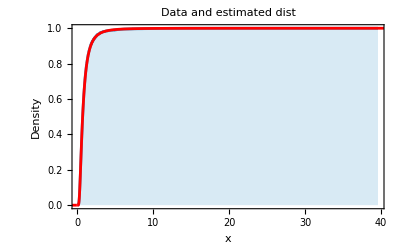

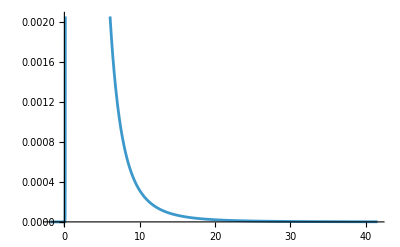

```mathematica
fileName=FileNameJoin[{path,"RND-inverseGamma.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, InverseGammaDistribution[k,θ]]
dist=InverseGammaDistribution[k /.est,θ /.est];
{xmin,xmax}={Min[data],Max[data]};
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,xmax+pad},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[PDF[dist,x],{x,xmin-pad,xmax+pad}]
```

{μ→-0.737864,β→0.652041}

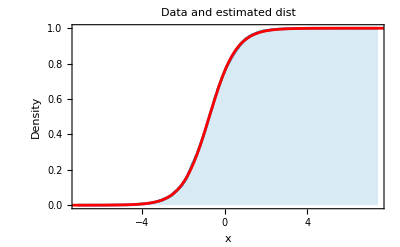

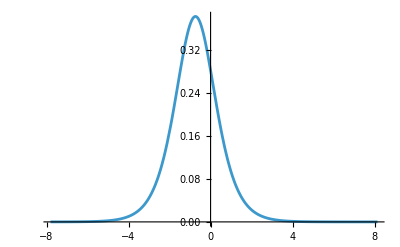

```mathematica
fileName=FileNameJoin[{path,"RND-logistic.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, LogisticDistribution[μ,β]]
dist=LogisticDistribution[μ /.est,β /.est];
{xmin,xmax}={Min[data],Max[data]};
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,xmax+pad},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[PDF[dist,x],{x,xmin-pad,xmax+pad}]
```

{α→2.82685,β→2.48529,λ→2.74522}

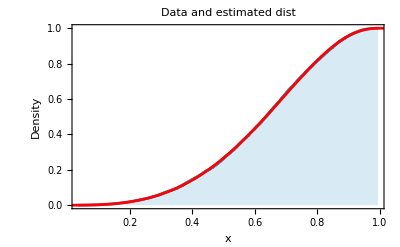

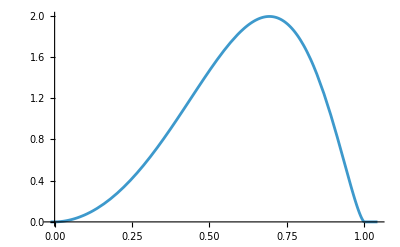

```mathematica
fileName=FileNameJoin[{path,"RND-nc-beta.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, NoncentralBetaDistribution[α,β,λ]]
dist=NoncentralBetaDistribution[α /.est,β /.est, λ /.est];
{xmin,xmax}={Min[data],Max[data]};
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,xmax+pad},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[PDF[dist,x],{x,xmin-pad,xmax+pad}]
```

{ν→5.9021,λ→5.15584}

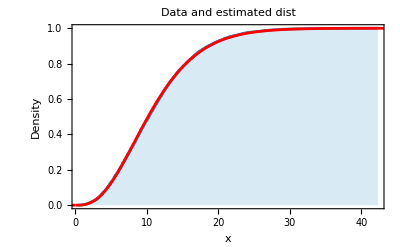

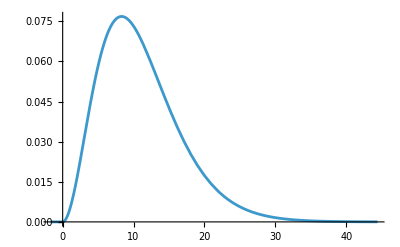

```mathematica
fileName=FileNameJoin[{path,"RND-nc-chiSquare.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, NoncentralChiSquareDistribution[ν,λ]]
dist=NoncentralChiSquareDistribution[ν /.est, λ /.est];
{xmin,xmax}={Min[data],Max[data]};
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,xmax+pad},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[PDF[dist,x],{x,xmin-pad,xmax+pad}]
```

{λ→3.52807}

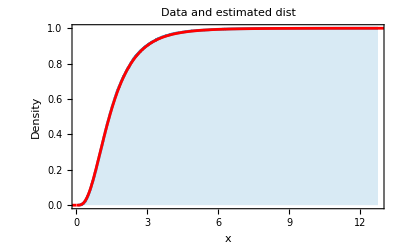

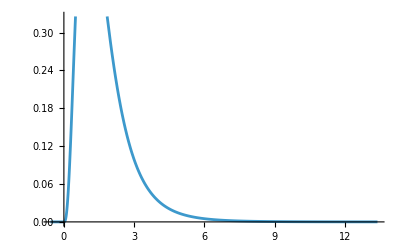

```mathematica
fileName=FileNameJoin[{path,"RND-nc-fisher.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, NoncentralFRatioDistribution[8, 16,λ]]
dist=NoncentralFRatioDistribution[8,16, λ /.est];
{xmin,xmax}={Min[data],Max[data]};
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,xmax+pad},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[PDF[dist,x],{x,xmin-pad,xmax+pad}]
```

{δ→5.01938}

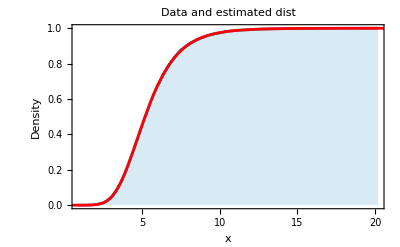

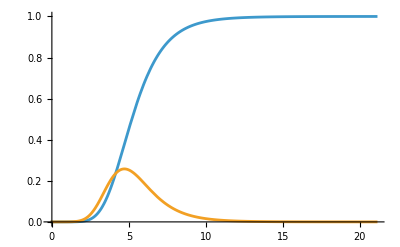

```mathematica
fileName=FileNameJoin[{path,"RND-nc-student.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, NoncentralStudentTDistribution[9,δ]]
dist=NoncentralStudentTDistribution[9,δ /. est];
{xmin,xmax}={Min[data],Max[data]};
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,xmax+pad},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[{CDF[dist,x],PDF[dist,x]},{x,xmin-pad,xmax+pad}]
```

{ξ→-0.21684,σ→1.11572,α→3.11042}

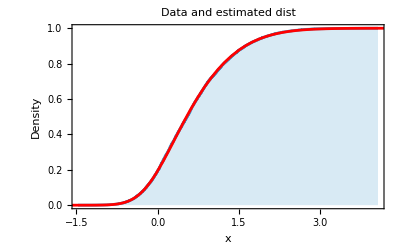

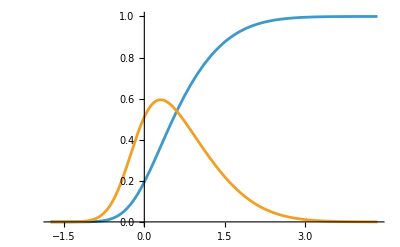

```mathematica
fileName=FileNameJoin[{path,"RND-skewNormal.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, SkewNormalDistribution[ξ,σ,α]]
dist=SkewNormalDistribution[ξ /. est, σ /. est, α/.est];
{xmin,xmax}={Min[data],Max[data]};
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,xmax+pad},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[{CDF[dist,x],PDF[dist,x]},{x,xmin-pad,xmax+pad}]
```

{μ→2.89473,c→4.6954}

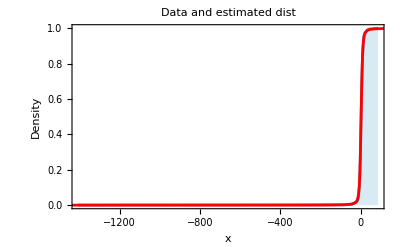

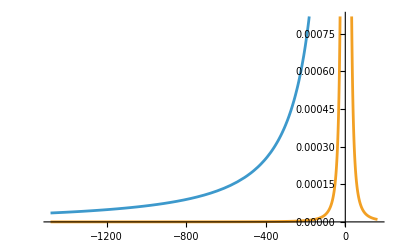

```mathematica
fileName=FileNameJoin[{path,"RND-holtsmark.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, StableDistribution[3/2,0,μ,c]]
dist=StableDistribution[3/2,0,μ /. est, c/.est];
{xmin,xmax}={Min[data],Max[data]};
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,xmax+pad},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[{CDF[dist,x],PDF[dist,x]},{x,xmin-pad,xmax+pad}]
```

FindMaximum::steperr: Error in step computation.

{μ→-0.342031,c→0.635808}

{-81.8031,1795.01}

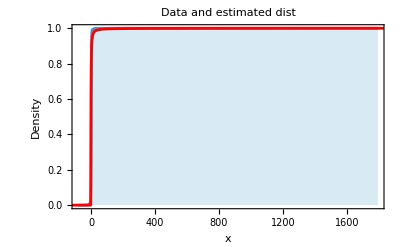

General::unfl: Underflow occurred in computation.

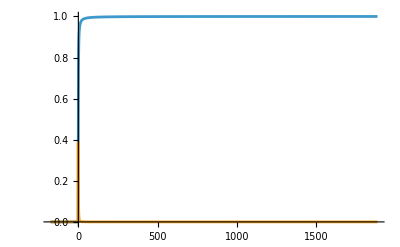

```mathematica
fileName=FileNameJoin[{path,"RND-Landau.csv"}];
data = Import[fileName][[1]];
edist=EmpiricalDistribution[data];
est=FindDistributionParameters[data, StableDistribution[1,1,1,μ,c]]
dist=StableDistribution[1,1,1,μ /. est, c/.est];
{xmin,xmax}={Min[data],Max[data]}
pad=0.05 (xmax-xmin);
kde=DiscretePlot[CDF[edist, x],{x, data}];
fit=Plot[CDF[dist,x],{x,xmin-pad,xmax+pad},PlotRange->All,PlotStyle->Red];
Show[kde,fit,Frame->True,FrameLabel->{"x","Density"},PlotLabel->"Data and estimated dist"]
Plot[{CDF[dist,x],PDF[dist,x]},{x,xmin-pad,xmax+pad}]
```